# Analyses données accélérométriques du K4 - 1000 m 2013

## Taux de déviation des cycles par rapport au cycle moyen sur la course

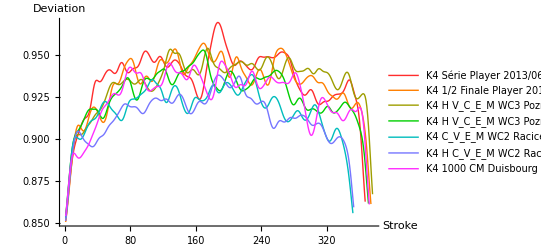

```mathematica
ListPlot[Table[Power[6+applylowpassfilter[Log[1-getData[dataproc,i,"Forward Acceleration Garbage Rate (Stroke)"]],10],-0.1],{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Stroke","Deviation"} ,PlotStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom],ImageSize->Full]
```

## Amplitude RMS de l’oscillation en gîte

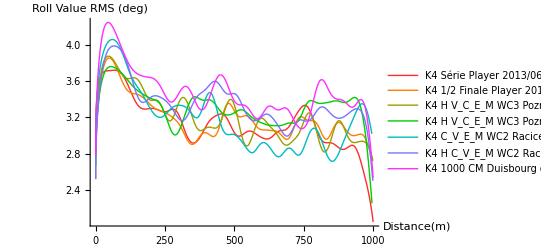

```mathematica
ListPlot[Table[Transpose[{
getData[dataproc,i,"Forward Distance"],
Power[applylowpassfilter[Power[applyhighpassfilter[getData[dataproc,i,"Roll Angle"],500],2],1000],1/2]*180/π
}],{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Distance(m)","Roll Value RMS (deg)"} ,PlotStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom],ImageSize->Full]
```

## Variation de la composante continue en gîte

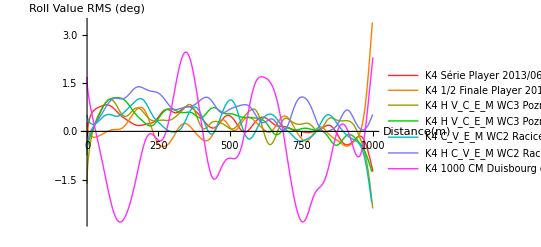

```mathematica
ListPlot[Table[Transpose[{
getData[dataproc,i,"Forward Distance"],
applylowpassfilter[getData[dataproc,i,"Roll Angle"],1000]*180/π
}],{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Distance(m)","Roll Value RMS (deg)"} ,PlotStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom],ImageSize->Full]
```

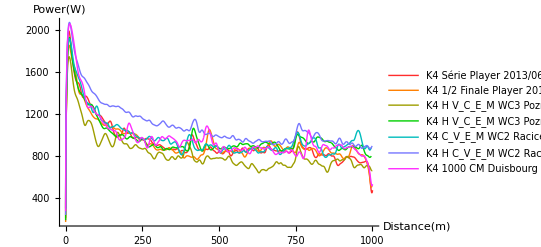

```mathematica
ListPlot[Table[Transpose[{
getData[dataproc,i,"Forward Distance"],
applylowpassfilter[getData[dataproc,i,"Total Power"],200]
}],{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Distance(m)","Power(W)"} ,PlotStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom],ImageSize->Full]
```

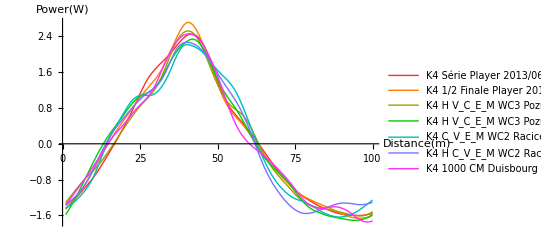

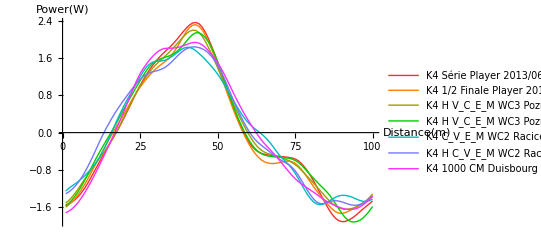

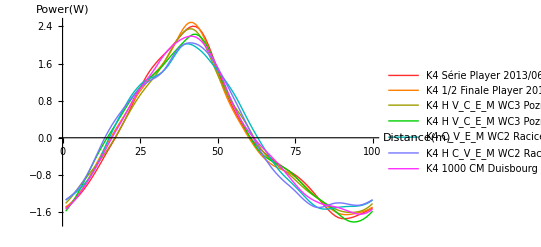

```mathematica
ListPlot[Table[

Mean[normalizelength[Take[getData[dataproc,i,"Forward Acceleration (Stroke)"],{1,-1,2}]]]

,{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Distance(m)","Power(W)"} ,PlotStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom],ImageSize->Full]
ListPlot[Table[

Mean[normalizelength[Take[getData[dataproc,i,"Forward Acceleration (Stroke)"],{2,-1,2}]]]

,{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Distance(m)","Power(W)"} ,PlotStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom],ImageSize->Full]

ListPlot[Table[

Mean[normalizelength[getData[dataproc,i,"Forward Acceleration (Stroke)"]]]

,{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Distance(m)","Power(W)"} ,PlotStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom],ImageSize->Full]
```

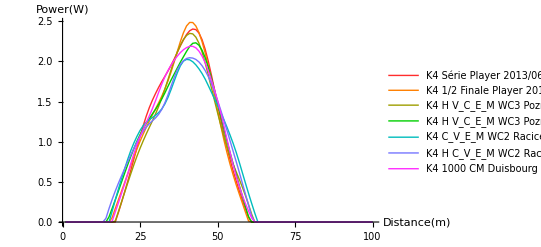

```mathematica
ListPlot[Table[

Map[Function[x,Max[x,0]],Mean[normalizelength[getData[dataproc,i,"Forward Acceleration (Stroke)"]]]]

,{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Distance(m)","Power(W)"} ,PlotStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom],ImageSize->Full]
```

```mathematica
Table[
Total@
Map[Function[x,Max[x,0]],Mean[normalizelength[getData[dataproc,i,"Forward Acceleration (Stroke)"]]]]

,{i,1,Length[getData[dataimport]]}]
```

{58.757,57.6063,56.1299,57.584,57.3758,57.2894,58.0417}

```mathematica
Total[{58.75701118244572,57.60632007681788,56.12985391517083,57.583975263878116,57.37576748625145,57.289412119764286,58.041722000252165}]
```

402.784

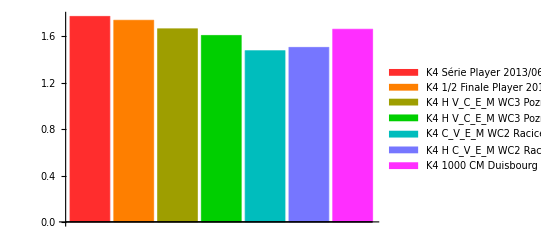

```mathematica
BarChart[Table[
Total@Map[Function[x,Max[x,0]^2],Mean[normalizelength[getData[dataproc,i,"Forward Acceleration (Stroke)"]]]]/
Total@Map[Function[x,Max[x,0]],Mean[normalizelength[getData[dataproc,i,"Forward Acceleration (Stroke)"]]]] 

,{i,1,Length[getData[dataimport]]}],
ChartStyle->Map[Function[x,RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[x,"LUV"],{2,3}]],"LUV"->"RGB"]],{Red,Orange,Yellow,Green,Cyan,Blue,Magenta}],
ChartLegends->Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]]]
```